# Label Predictions Sezin Yaman April, May 2018

I specifically used a package called MonadicContextualClassification, that provides functions for classification with classifiers with contexts and the documentation can be found here. The package is also discussed in this community forum. The figure below outlines the classification process in the pipeline.

           -Graphics-

Mathematica is a computation program well known for technical computing such as machine learning and it uses Wolfram language, that is a multi-paradigm, functional language. In the rest of the notebook we start with data load and wrangling (Chapter 1 and Chapter 2), continue with several dimension reduction attempts on the training data and training the classifiers accordingly (Chapter 3). We also present the prediction results in Section 3.3.4. Lastly, we do comparisons on classifiers and sum up the learnings (Chapter 4).

## 1. Data load

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MonadicProgramming/MonadicContextualClassification.m"];
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"];
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MosaicPlot.m"];
```

```mathematica
Training= Import["/Users/yaman/Desktop/homework_48/train_data.csv"];
Tlabels= Import["/Users/yaman/Desktop/homework_48/train_labels.csv"];
testingCSVData= Import["/Users/yaman/Desktop/homework_48/test_data.csv"];

Dimensions[Training]
Dimensions[Tlabels]
Dimensions[testingCSVData]
```

{3750,10000}

{3750,1}

{1250,10000}

## 2. Data wrangling

```mathematica
Tally[Tlabels] 
mlData=MapThread[Rule,{Training,Tlabels⟦All,1⟧}];
Short/@mlData⟦1;;6⟧
```

{{{1},3378},{{-1},372}}

{{620.643,-225.484,-131214.,83536.7,«9993»,133.456,-344.193,626.785}→1,{789.336,158.857,-8422.37,54747.6,«9992»,32.379,-418.297,-292.736,-390.922}→1,{-323.514,-520.415,-43709.2,150098.,«9993»,-684.42,-1878.7,-31.079}→1,{280.384,4.955,-13609.3,-141966.,«9993»,-496.787,-205.806,-240.249}→1,{15.483,-98.902,37406.,138522.,«9993»,-650.591,-45.142,678.672}→1,{575.561,-345.999,28541.3,20939.8,«9993»,-232.023,-436.482,-158.154}→1}

Now we merged labels with the training data and put it in the right form. One observation is that the labels are mostly 1’s. Dimension reduction could be wise to apply.

## 3. Attempts with dimension reduction

### 3.1 First try with 12 dimensions

In this section, let’s first try apply low-rank SVD to the training data in order to reduce the dimension to 12 basis vectors and train a classifier.

```mathematica
RecordsSummary[Mean[mlData⟦All,1⟧]]
```

{1 column 1
Min | -752.913
1st Qu | 9.07144
Median | 14.4814
3rd Qu | 20.1494
Mean | 25.3132
Max | 85695.5}

Apply SVD on training data:

```mathematica
svdRes0=SingularValueDecomposition[mlData⟦All,1⟧,12];
```

```mathematica
Dimensions/@svdRes0
```

{{3750,12},{12,12},{10000,12}}

Transform the data:

```mathematica
mlData2=MapThread[Rule,{svdRes0⟦1⟧,Tlabels⟦All,1⟧}];
RecordsSummary[mlData2,Thread->True]
Short/@mlData2⟦1;;6⟧
```

{1 column 1
Min | -0.0381579
1st Qu | -0.0210219
Median | -0.00738576
Mean | -0.00720428
3rd Qu | 0.00662302
Max | 0.0242548,2 column 2
Min | -0.0565906
1st Qu | -0.0111527
Mean | -0.000159545
Median | -0.000100279
3rd Qu | 0.0111871
Max | 0.0557858,3 column 3
Min | -0.052951
1st Qu | -0.0107632
Median | -0.000132896
Mean | -0.0000214609
3rd Qu | 0.0109954
Max | 0.0575035,4 column 4
Min | -0.0599539
1st Qu | -0.0110121
Mean | 0.000205514
Median | 0.00029938
3rd Qu | 0.0110236
Max | 0.0598682,5 column 5
Min | -0.061953
1st Qu | -0.010073
Median | 0.000720162
Mean | 0.000934545
3rd Qu | 0.0118416
Max | 0.0710834,6 column 6
Min | -0.0297199
1st Qu | 0.00227527
Median | 0.0107471
Mean | 0.0108286
3rd Qu | 0.0190886
Max | 0.0555419,7 column 7
Min | -0.0594535
1st Qu | -0.0111447
Mean | -0.000328781
Median | -0.000220589
3rd Qu | 0.0107263
Max | 0.052272,8 column 8
Min | -0.0592629
1st Qu | -0.0113856
Median | -0.000422077
Mean | -0.000300383
3rd Qu | 0.0107644
Max | 0.0558449,9 column 9
Min | -0.059068
1st Qu | -0.0111331
Mean | -0.0000339777
Median | 0.0000995472
3rd Qu | 0.0108988
Max | 0.0591568,10 column 10
Min | -0.055769
1st Qu | -0.0108419
Median | -0.000127776
Mean | 0.000178098
3rd Qu | 0.0115082
Max | 0.068682,11 column 11
Min | -0.0544622
1st Qu | -0.0112319
Mean | -0.000364756
Median | -0.000239868
3rd Qu | 0.0104151
Max | 0.0664438,12 column 12
Min | -0.0543678
1st Qu | -0.0116429
Mean | -0.000676484
Median | -0.000644835
3rd Qu | 0.0107174
Max | 0.0577258}→{1 column 1
Min | -1
Mean | 0.8016
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

{{-0.0196666,0.0181426,«8»,0.00563199,-0.00951586}→1,{0.0101886,0.0118767,«8»,-0.0213271,-0.00476392}→1,{-0.0000171904,0.0312215,«8»,0.0147743,0.0444562}→1,{-0.016201,-0.0264471,«8»,-0.0117296,-0.0140664}→1,{-0.0245408,0.0242427,«8»,0.00435455,-0.0121917}→1,{0.00508833,0.00389178,«8»,0.00909727,0.0153733}→1}

Just checking the matrices:

```mathematica
Dimensions[Transpose[svdRes0⟦3⟧]]
```

{12,10000}

```mathematica
(Transpose[svdRes0⟦3⟧].mlData⟦All,1⟧⟦1⟧).Inverse[svdRes0⟦2⟧]
```

{-0.0196666,0.0181426,-0.000189024,0.030512,-0.00589098,0.00772635,0.00553564,-0.00243173,0.00881216,-0.00323336,0.00563199,-0.00951586}

```mathematica
(svdRes0⟦2⟧.Transpose[svdRes0⟦3⟧]).mlData⟦All,1⟧⟦1⟧
```

{-2.98112×10^12,4.71313×10^11,-3.86983×10^9,5.26083×10^11,-4.69739×10^9,1.03906×10^8,6.83239×10^7,-2.98397×10^7,1.07748×10^8,-3.94221×10^7,6.82547×10^7,-1.15225×10^8}

Now using the pipeline to get the classifier trained and see the performance:

summaries: {trainingData→{1 RowID
1 | 13
10 | 13
100 | 13
1000 | 13
1001 | 13
1002 | 13
(Other) | 38909,2 Variable
1 | 2999
10 | 2999
11 | 2999
12 | 2999
13 | 2999
2 | 2999
(Other) | 20993,3 Value
Min | -1
1st Qu | -0.0103231
Median | 0.00222063
3rd Qu | 0.0142016
Mean | 0.0619617
Max | 1},testData→{1 RowID
1 | 13
10 | 13
100 | 13
101 | 13
102 | 13
103 | 13
(Other) | 9685,2 Variable
1 | 751
10 | 751
11 | 751
12 | 751
13 | 751
2 | 751
(Other) | 5257,3 Value
Min | -1
1st Qu | -0.0104268
Median | 0.00193534
3rd Qu | 0.0140685
Mean | 0.061637
Max | 1}}

Classifier information
Method | Random forest
Number of classes | 2
Number of features | 1
Number of training examples | 2999
Number of trees | 50

value: <|Accuracy→0.960053,Precision→<|-1→0.868852,1→0.968116|>,Recall→<|-1→0.706667,1→0.988166|>|>

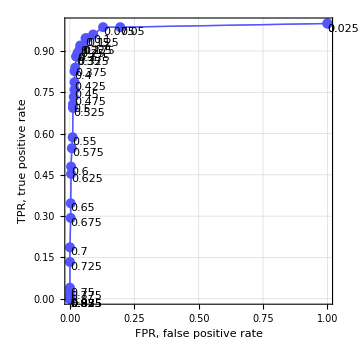
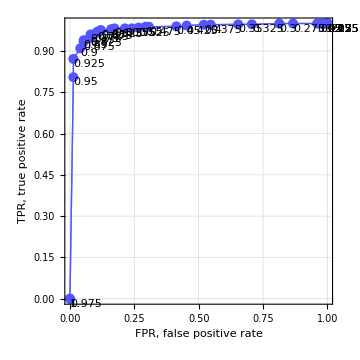
ROC plot(s): <|-1→-Graphics-,1→-Graphics-|>

value: <|None→0.960053,1→0.829561,2→0.960053,3→0.958722,4→0.956059,5→0.950732,6→0.95739,7→0.956059,8→0.962716,9→0.961385,10→0.958722,11→0.958722,12→0.958722|>

```mathematica
res1 = ClConUnit[mlData2]⟹
ClConModifyContext[Join[#,<|"variableNames"->Map[ToString,Range[Length[mlData2⟦1,1⟧]+1]]|>]&]⟹
ClConSplitData[0.8]⟹
ClConAddToContext⟹
ClConSummarizeData[]⟹
ClConMakeClassifier["RandomForest"]⟹
ClConEchoFunctionContext[Magnify[ClassifierInformation[#["classifier"]],0.6]&]⟹
ClConClassifierMeasurements[{"Accuracy","Precision","Recall"}]⟹
ClConEchoValue⟹
ClConROCPlot[]⟹
ClConAccuracyByVariableShuffling[]⟹
ClConEchoValue;
```

We extract the classifier:

```mathematica
cf1=res1⟹ClConTakeClassifier
```

ClassifierFunction[…]

### 3.2 Separation before transformation (study phase)

In this section let’s split the data before transformation and try more with SVD. We will utilize the SVD in two study ways: in the first study we extract the most decisive vectors and filter the training set based on them (Section 3.2.1). in the second study we go with predefined dimension space, and use validation data for classification pipeline (Section 3.2.2).

#### 3.2.1 Most significant vectors

```mathematica
mlData=MapThread[Rule,{Training,Tlabels⟦All,1⟧}];
```

Separating the data at 0.75:

```mathematica
SeedRandom[123]
{trainingData,testData}=TakeDrop[RandomSample[mlData],Floor[0.75*Length[mlData]]];
```

```mathematica
meanRow=Mean[trainingData⟦All,1⟧];
RecordsSummary[meanRow]
```

{1 column 1
Min | -1131.99
1st Qu | 8.22631
Median | 14.6834
3rd Qu | 20.9983
Mean | 25.0205
Max | 83377.9}

apply SVD:

```mathematica
svdRes=SingularValueDecomposition[Map[#-meanRow&,trainingData⟦All,1⟧],120];
```

Let’s see the most significant ones on a plot:

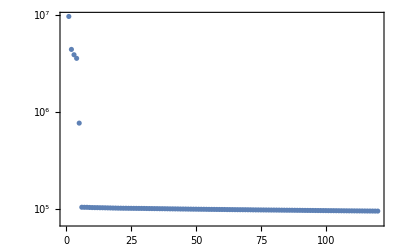

```mathematica
ListLogPlot[Diagonal[svdRes⟦2⟧],PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
RecordsSummary[svdRes⟦3,All,1⟧]
```

{1 column 1
Min | -0.000354587
1st Qu | -0.0000316648
Median | 4.11535×10^-7
3rd Qu | 0.0000316302
Mean | 0.000123808
Max | 0.969048}

We can get the positions of most representative vectors:

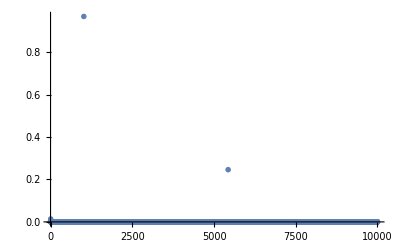

```mathematica
ListPlot[Abs[svdRes⟦3,All,1⟧],PlotRange->All,PlotStyle->{PointSize[0.01]}]
```

```mathematica
pos=Flatten@Position[Abs[svdRes⟦3,All,1⟧],x_/;x>0.1]
```

{1018,5433}

Transform the data with those vectors:

variable names: {1,2,3}

Classifier information
Method | Random forest
Number of classes | 2
Number of features | 1
Number of training examples | 2812
Number of trees | 50

value: <|Accuracy→0.96162,Precision→<|-1→0.833333,1→0.977273|>,Recall→<|-1→0.817308,1→0.979616|>|>

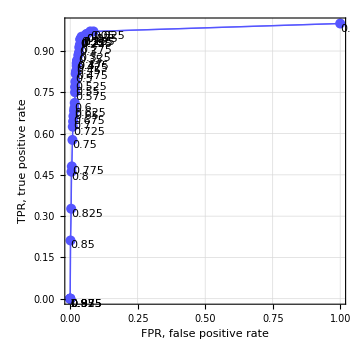
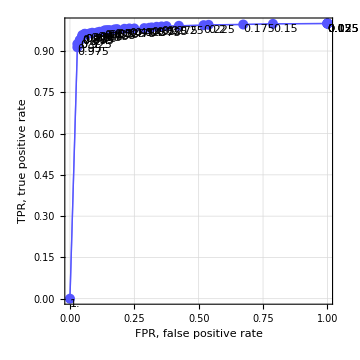
ROC plot(s): <|-1→-Graphics-,1→-Graphics-|>

value: <|Accuracy→0.959488,Precision→<|-1→0.761905,1→0.990148|>,Recall→<|-1→0.923077,1→0.964029|>|>

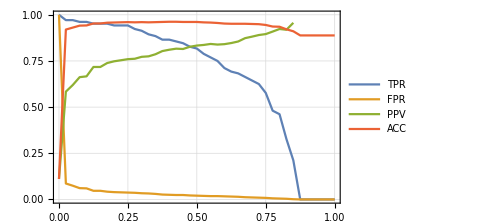
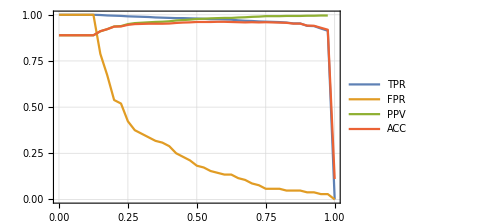
ROC line plot(s): <|-1→-Graphics-,1→-Graphics-|>

value: <|None→0.96162,1→0.50533,2→0.491471|>

```mathematica
trainingData2=Thread[(trainingData⟦All,1⟧⟦All,pos⟧)->trainingData⟦All,2⟧];
testData2=Thread[(testData⟦All,1⟧⟦All,pos⟧)->testData⟦All,2⟧];

res=
ClConUnit[<|"trainingData"->trainingData2,"testData"->testData2|>]⟹
ClConAddToContext⟹
ClConAssignVariableNames[]⟹
ClConEchoVariableNames[]⟹
ClConMakeClassifier["RandomForest"]⟹
ClConEchoFunctionContext[Magnify[ClassifierInformation[#["classifier"]],0.8]&]⟹
ClConClassifierMeasurements[]⟹ClConEchoValue⟹
ClConROCPlot[]⟹
ClConClassifierMeasurementsByThreshold[{"Accuracy","Precision","Recall"},-1->0.275]⟹ClConEchoValue⟹
ClConROCListLinePlot[{"TPR","FPR","PPV","ACC"}]⟹
ClConAccuracyByVariableShuffling[]⟹
ClConEchoValue;
```

Extract classify function for later use:

```mathematica
cf2=First@Values[res⟹ClConTakeClassifier]
```

ClassifierFunction[…]

#### 3.2.2 SVD with 7 dimensions

Let’s also try SVD with 7 dimensions:

```mathematica
svdRes2=SingularValueDecomposition[trainingData⟦All,1⟧,7];
```

U_training.S_training.V_training^T = M_training

Transform the training data accordingly:

```mathematica
trainingData3=Thread[svdRes2⟦1⟧.svdRes2⟦2⟧->trainingData⟦All,2⟧];
RecordsSummary[trainingData3,Thread->True]
```

{1 column 1
Min | -298465.
1st Qu | -84088.2
Median | 80025.2
Mean | 86291.3
3rd Qu | 258231.
Max | 469033.,2 column 2
Min | -288246.
1st Qu | -55974.5
Mean | -813.065
Median | 138.512
3rd Qu | 58351.3
Max | 275836.,3 column 3
Min | -238981.
1st Qu | -48335.8
Median | -536.749
Mean | 165.231
3rd Qu | 49267.7
Max | 266371.,4 column 4
Min | -242301.
1st Qu | -44312.6
Mean | 1313.4
Median | 1879.07
3rd Qu | 46498.6
Max | 247579.,5 column 5
Min | -55310.8
1st Qu | -9052.99
Median | 491.734
Mean | 817.687
3rd Qu | 10629.
Max | 63476.4,6 column 6
Min | -4251.33
1st Qu | 216.514
Median | 1286.93
Mean | 1289.78
3rd Qu | 2350.72
Max | 7472.42,7 column 7
Min | -7382.6
1st Qu | -1348.82
Mean | 4.49685
Median | 28.7751
3rd Qu | 1312.73
Max | 7103.8}→{1 column 1
Min | -1
Mean | 0.809388
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

Checking the dimensions:

```mathematica
Dimensions[Transpose[svdRes2⟦3⟧]]
Dimensions[testData⟦All,1⟧]
```

{7,10000}

{938,10000}

Apply the data transformation (dimension reduction by SVD) to the test data part. Note that the SVD matrices used in the transformation were obtained from the training data only.

```mathematica
testData3=(testData⟦All,1⟧.svdRes2⟦3⟧).Inverse[svdRes2⟦2⟧];
testData3=Thread[testData3->testData⟦All,2⟧];
RecordsSummary[testData3,Thread->True]
```

{1 column 1
Min | -0.0240018
1st Qu | -0.00703041
Mean | 0.00899725
Median | 0.0103261
3rd Qu | 0.0245722
Max | 0.0423416,2 column 2
Min | -0.0541148
1st Qu | -0.0130513
Median | -0.000618487
Mean | -0.000161726
3rd Qu | 0.0121271
Max | 0.0645679,3 column 3
Min | -0.0639481
1st Qu | -0.0125033
Median | -0.000142361
Mean | 0.000252131
3rd Qu | 0.0135501
Max | 0.0634837,4 column 4
Min | -0.070204
1st Qu | -0.0132991
Median | -0.000739836
Mean | -0.000333725
3rd Qu | 0.0126869
Max | 0.0645032,5 column 5
Min | -0.0669441
1st Qu | -0.0108033
Mean | 0.00138746
Median | 0.00160622
3rd Qu | 0.0137321
Max | 0.0747202,6 column 6
Min | -0.0169354
1st Qu | 0.00106553
Mean | 0.0062887
Median | 0.00640261
3rd Qu | 0.0117367
Max | 0.0286047,7 column 7
Min | -0.0294562
1st Qu | -0.00526424
Mean | 0.0000276345
Median | 0.00016977
3rd Qu | 0.00547389
Max | 0.0271276}→{1 column 1
Min | -1
Mean | 0.778252
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

Running the classification workflow:

```mathematica
Dimensions[trainingData3]
Dimensions[testData3]
```

{2812}

{938}

This time let’s only use the classify function:

```mathematica
cf3=Classify[trainingData3,Method->"RandomForest",ValidationSet->testData3]
```

ClassifierFunction[…]

### 3.3 Full cycle

Here finally we will use the unseen test set. But first, we treat mlData as training data and apply SVD with 8 dimensions (Section 3.3.1). Second, we build a classifier with both with a validation set and without (Section 3.3.2). Next we transform unseen test data in the reduced space (Section 3.3.3). Finally 3.3.4 will present the prediction results of selected classifiers.

#### 3.3.1 Dimension reduction on the training data

```mathematica
mlData=MapThread[Rule,{Training,Tlabels⟦All,1⟧}];
Short/@mlData⟦1;;6⟧
```

{{620.643,-225.484,-131214.,83536.7,«9993»,133.456,-344.193,626.785}→1,{789.336,158.857,-8422.37,«9994»,-418.297,-292.736,-390.922}→1,{-323.514,-520.415,-43709.2,150098.,«9993»,-684.42,-1878.7,-31.079}→1,{280.384,4.955,-13609.3,-141966.,«9993»,-496.787,-205.806,-240.249}→1,{15.483,-98.902,37406.,138522.,«9993»,-650.591,-45.142,678.672}→1,{575.561,-345.999,28541.3,20939.8,«9993»,-232.023,-436.482,-158.154}→1}

```mathematica
trainingDataFull=mlData;
```

```mathematica
AbsoluteTiming[
svdRes3=SingularValueDecomposition[trainingDataFull⟦All,1⟧,8];
]
```

{29.1597,Null}

```mathematica
trainingData4=Thread[svdRes3⟦1⟧.svdRes3[[2]]->trainingDataFull⟦All,2⟧];
```

```mathematica
RecordsSummary[trainingData4,Thread->True]
```

{1 column 1
Min | -469797.
1st Qu | -258819.
Median | -90932.8
Mean | -88698.5
3rd Qu | 81541.9
Max | 298622.,2 column 2
Min | -288436.
1st Qu | -56844.
Mean | -813.184
Median | -511.109
3rd Qu | 57019.6
Max | 284334.,3 column 3
Min | -239586.
1st Qu | -48699.9
Median | -601.313
Mean | -97.1035
3rd Qu | 49750.4
Max | 260185.,4 column 4
Min | -248948.
1st Qu | -45725.9
Mean | 853.363
Median | 1243.13
3rd Qu | 45773.6
Max | 248593.,5 column 5
Min | -55321.8
1st Qu | -8994.85
Median | 643.08
Mean | 834.516
3rd Qu | 10574.2
Max | 63475.,6 column 6
Min | -3446.52
1st Qu | 263.856
Median | 1246.31
Mean | 1255.75
3rd Qu | 2213.64
Max | 6441.02,7 column 7
Min | -6605.1
1st Qu | -1238.15
Mean | -36.5265
Median | -24.5068
3rd Qu | 1191.65
Max | 5807.26,8 column 8
Min | -6564.82
1st Qu | -1261.23
Median | -46.7553
Mean | -33.2748
3rd Qu | 1192.43
Max | 6186.18}→{1 column 1
Min | -1
Mean | 0.8016
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

#### 3.3.2 Classifier building

We can create a classifier with a validation set (cf4), and also one without (cf5); and also one with using the pipeline (cf6).

```mathematica
{trainingData5,validationData5}=TakeDrop[trainingData4,Floor[0.9*Length[trainingDataFull]]];
Length/@{trainingData5,validationData5}
```

{3375,375}

```mathematica
cf4=Classify[trainingData5,Method->"RandomForest",ValidationSet->validationData5]
```

ClassifierFunction[…]

Let’s train one without validation set:

```mathematica
cf5=Classify[trainingData4,Method->"RandomForest"]
```

ClassifierFunction[…]

Also one using the pipeline:

```mathematica
res5=
ClConUnit[<|"trainingData"->trainingData5,"testData"->{},"validationData"->validationData5|>]⟹
ClConAddToContext⟹
ClConMakeClassifier["RandomForest"];
```

```mathematica
cf6=res5⟹ClConTakeClassifier
```

ClassifierFunction[…]

#### 3.3.3 Transforming the unseen test data in reduced space

Finally we can transform the unseen test data, reduce it and call the classifier.

Checking the dimensions and the matrices first:

```mathematica
Dimensions[testingCSVData]
```

{1250,10000}

U_training.S_training.V_training^T = M_traning

```mathematica
Dimensions[svdRes3⟦3⟧]
```

{10000,8}

```mathematica
Diagonal[svdRes3⟦2⟧]
```

{1.23119×10^7,5.09689×10^6,4.52467×10^6,4.15233×10^6,892965.,115967.,111097.,110774.}

```mathematica
Norm/@Transpose[svdRes3⟦3⟧]
```

{1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
t=SparseArray[Transpose[svdRes3⟦3⟧]].SparseArray[svdRes3⟦3⟧];
MatrixForm[Chop[t]]
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Dimensions[testingCSVData]
```

{1250,10000}

```mathematica
testData5=testingCSVData.svdRes3⟦3⟧;
Dimensions[testData5]
```

{1250,8}

```mathematica
RecordsSummary[testData5]
```

{1 column 1
Min | -456583.
1st Qu | -264728.
Median | -94690.2
Mean | -92109.1
3rd Qu | 87497.4
Max | 273814.,2 column 2
Min | -331949.
1st Qu | -55277.1
Median | -2572.99
Mean | -1251.77
3rd Qu | 56217.4
Max | 268400.,3 column 3
Min | -245419.
1st Qu | -52984.9
Median | -5156.78
Mean | -4096.25
3rd Qu | 47778.6
Max | 267045.,4 column 4
Min | -220967.
1st Qu | -45230.9
Median | -1497.8
Mean | -147.141
3rd Qu | 47327.6
Max | 218209.,5 column 5
Min | -52090.5
1st Qu | -9402.93
Mean | 430.155
Median | 878.368
3rd Qu | 10108.
Max | 43931.8,6 column 6
Min | -2249.95
1st Qu | 179.617
Mean | 768.857
Median | 803.611
3rd Qu | 1353.85
Max | 3590.84,7 column 7
Min | -2721.42
1st Qu | -639.375
Mean | -57.5662
Median | -10.2156
3rd Qu | 500.986
Max | 2968.34,8 column 8
Min | -2861.63
1st Qu | -661.53
Median | -104.336
Mean | -83.8895
3rd Qu | 482.929
Max | 2648.53}

```mathematica
RecordsSummary[trainingData5,Thread->True]
```

#### 3.3.4 Classification results

Here are the final classification results beginning from the classifiers we built in full cycle (cf4, cf5 and cf6). After that we can also check the previous classifiers trained by seen training data (cf1, cf2 and cf3).

This one below is the one we built using the pipeline and validation set:

```mathematica
clResult6=cf6[testData5];
Short[clResult6]
RecordsSummary[clResult6]
Tally[clResult6]
(*Export["test_labels2_new.csv", clResult6]*)
```

{1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,«1198»,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,-1,1,1,1,1,-1,1,1,1,1,1,1}

{1 column 1
Min | -1
Mean | 0.8208
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

{{1,1138},{-1,112}}

test_labels2_new.csv

This one below is the one we built using the Mathematica’s classify function and WITHOUT a validation set:

```mathematica
clResult5=cf5[testData5];
Short[clResult5]
RecordsSummary[clResult5]
Tally[clResult5]
```

{1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,«1213»,1,1,1,1,-1,1,-1,1,1,1,1,-1,1,1,1,1,1,1}

{1 column 1
Min | -1
Mean | 0.8176
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

{{1,1136},{-1,114}}

The below is the one we built using the Mathematica’s classify function and with a validation set:

```mathematica
clResult4=cf4[testData5];
Short[clResult4]
RecordsSummary[clResult4]
Tally[clResult4]
(*Export["test_labels_new.csv", clResult4]*)
```

{1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,«1198»,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,-1,1,1,1,1,-1,1,1,1,1,1,1}

{1 column 1
Min | -1
Mean | 0.8144
1st Qu | 1
3rd Qu | 1
Max | 1
Median | 1}

{{1,1134},{-1,116}}

test_labels_new.csv

```mathematica
clResult3=cf3[testData3];
Short[clResult3]
RecordsSummary[clResult3]
Tally[clResult3]
```

#### 4. Comparisons, Learnings and Workload

So far we only know that cf4, cf5 and cf6 predicts different labels for the test data.

```mathematica
clRes=Transpose[{cf5[testData5],cf6[testData5]}];
ct=CrossTabulate[clRes];
MatrixForm[ct]
```

( | -1 | 1
-1 | 106 | 8
1 | 6 | 1130)

```mathematica
clRes2=Transpose[{cf4[testData5],cf6[testData5]}];
ct2=CrossTabulate[clRes2];
MatrixForm[ct2]
```

( | -1 | 1
-1 | 109 | 7
1 | 3 | 1131)

```mathematica
clRes2=Transpose[{cf1[testData5],cf6[testData5]}];
ct2=CrossTabulate[clRes2];
MatrixForm[ct2]
```

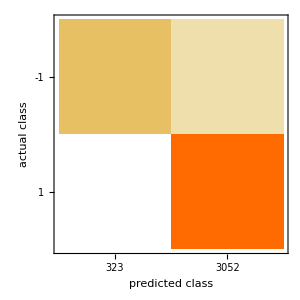

```mathematica
ClassifierMeasurements[cf4,trainingData5,"ConfusionMatrixPlot"]
```

```mathematica
ClassifierInformation[cf4]
```

Classifier information
Input type | NumericalVector (length: 8)
Classes | ,,-11
Method | RandomForest
Accuracy | 97. % ± 0.47 %
Loss | 0.126 ± 0.005
Single evaluation time | 5.06 ms/example
Batch evaluation speed | 27.7 examples/ms
Classifier memory | 245. kB
Training examples used | 3375 examples
Training time | 2.47 s
 |

The reason why Random Forest method was used is that it performed the best compared to other methods such as Logistic Regression. Based on the parameters such as accuracy, our classifiers seem to perform good. The question of whether the unseen test data is representative of training data is subject to further examination. 

In general we can conclude that the training data included noise that needed to be reduced in dimension space. We can argue that only some features, i.e., 2-5, are decisive, however, it is again subject to further examination whether they are only two vectors or distributed over multiple vectors. Regardless, two-vector dimension reduction and respective classification yielded okay results. Yet in the full cycle we went with 8 dimensions. cf4 could be a good classifier as it has good classification parameters and also that we used validation set with it.